## Setup and Initialization

The background code be loaded by the following (so long as “loop_amplitudes.m” is in the same directory as the notebook)

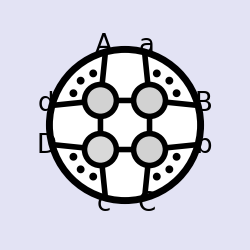
-Graphics-
One-Loop Amplitude Integrands
and Integrals in N=4 SYM
Jacob L. Bourjaily, 2013

```mathematica
SetDirectory[NotebookDirectory[]];
<<loop_amplitudes.m
```

If the file “loop_amplitudes.m” is copied to your Mathematica’s “Application” directory,

```mathematica
FileNameJoin[{$UserBaseDirectory,"Applications"}]
```

via the command,

```mathematica
If[FileExistsQ[FileNameJoin[{$UserBaseDirectory,"Applications","loop_amplitudes.m"}]],DeleteFile[FileNameJoin[{$UserBaseDirectory,"Applications","loop_amplitudes.m"}]]];CopyFile[FileNameJoin[{NotebookDirectory[],"loop_amplitudes.m"}],FileNameJoin[{$UserBaseDirectory,"Applications","loop_amplitudes.m"}]];
```

then “<<loop_amplitudes.m” can be used in any notebook without any further initialization.

## One-Loop Integrands

### BCFW Recursed Form of One-Loop Integrands

#### Example Gratia: The one-loop, 6-particle NMHV amplitude A_6^(1) computed via BCFW recursion

The ℓ-loop, n-point N^(k)MHV amplitude is computed using BCFW recursion by the function “rAmp[n_,k_,ℓ_]”:

```mathematica
egLoopIntegrand=rAmp[6,1,1];
nice@%
```

This can be converted to a collection of standard superfunctions using the function “fromRform[n_][expression_]” 
which—among other things—converts the symbolic 5-brackets R[a,b,c,d,e] into standard, evaluatable superfunctions.

```mathematica
egAnalyticIntegrand=fromRform[][egLoopIntegrand];
nice@random[%]
```

If f^(k) is a superfunction, it is associated with a pair {f,C} where f is an ordinary function and the matrix C encodes all the component-functions according to

We can evaluate the integrand for a particular component, at a given point in momentum-space by choosing some convenient reference twistors, using for example, the function “exampleTwistors[n_]”

```mathematica
exampleTwistors[6]
```

To see what twistors have been specified, use the function “showTwistors”

```mathematica
showTwistors
```

Now we are ready to evaluate the integrand at some point using the function “evaluate[expression_]”:

```mathematica
egNumericIntegrand=evaluate[egAnalyticIntegrand]
```

A particular component can be extracted using the function  “superComponent[component__][superFunction_].”
For example, the supercomponent proportional to (η_3)^4 would be computed as follows:

```mathematica
egComponentBCFW=superComponent[p,p,m,p,p,p][egNumericIntegrand]
```

### Chiral Box Expansion of One-Loop Integrands

The chiral box expansion provides an alternative way to represent all loop amplitude integrands in SYM

#### Example Gratia: The one-loop, 6-point NMHV amplitude integrand A_6^((1),1) computed via the chiral box expansion

A purely symbolic manifestation of the chiral box expansion is given by “chiralBoxExpansion[n_,k_]”:

```mathematica
egChiralBoxIntegrand=chiralBoxExpansion[6,1];
nice[%]
```

To make this a bit more intelligible, the cyclic “seeds” which generate the full expansion can be extracted using “onlyCyclicSeeds[expression_]”; and the contributions can be represented graphically using “nice[expression_]”:

```mathematica
egChiralSeeds=onlyCyclicSeeds[egChiralBoxIntegrand]
nice[%]
```

The purely symbolic objects appearing in this expression such as “chiralBox[_][legList_]” can be converted into analytic formulae using “integrand[expression_]”:

```mathematica
nice@integrand[chiralBox[2][{{2},{3},{4,5},{6,1}}]]
```

The function “analyticIntegrand[expression_]” converts all the symbolic objects—including the all instances of “onShellGraph[_][legList_]” “amp[n_,k_]” etc.—into canonical superfunctions of the form described above:

```mathematica
egAnalyticChiralBoxIntegrand=analyticIntegrand[egChiralBoxIntegrand];
nice[random[%]]
```

As before, this set of superfunctions can be evaluated at some point using the function “evaluate[expression_]”:

```mathematica
egNumericChiralBoxIntegrand=evaluate[egAnalyticChiralBoxIntegrand]
```

And as before, a particular component can be extracted using the function  “superComponent[component__][superFunction_].”
For example, the supercomponent proportional to (η_3)^4 would be computed using:

```mathematica
egChiralBoxComponent=superComponent[p,p,m,p,p,p][egNumericChiralBoxIntegrand]
```

And we can check that this matches the BCFW-component function:

```mathematica
egComponentBCFW
%==egChiralBoxComponent
```

And we see that the expansion works!

### Comparing the Chiral Box Expansion with BCFW-Recursion

#### Example: the 8-point N^2MHV integrand:

First, we must choose some arbitrary reference momentum-twistors:

```mathematica
exampleTwistors[8]
showTwistors
```

A more compact way to generate the numerically-evaluated BCFW loop integrand is to use the function “nAmp[n_,k_,ℓ_]”:

```mathematica
egBCFWAmp=timed[nAmp[8,2,1]];
```

(Notice that we have used the function “timed[expression_]” to time the evaluation process.)

Similarly, a more compact way to generate the numerically-evaluated chiral-box expanded form of the integreand is to use:

```mathematica
egChiralBoxAmp=timed[evaluate[chiralLoopIntegrand[8,2]]];
```

Let us compare these two integrands at the specified kinematical point for the component proportional to (η_3)^4(η_5)^4

```mathematica
egBCFWComponent=timed[superComponent[p,m,p,p,m,p,p,p][egBCFWAmp]]
```

```mathematica
egChiralBoxComponent=timed[superComponent[p,m,p,p,m,p,p,p][egChiralBoxAmp]]
```

```mathematica
egBCFWComponent==egChiralBoxComponent
```

#### Example: the 10-point N^3MHV integrand:

First, we must choose some arbitrary reference momentum-twistors:

```mathematica
exampleTwistors[10]
showTwistors
```

A more compact way to generate the numerically-evaluated BCFW loop integrand is to use the function “nAmp[n_,k_,ℓ_]”:

```mathematica
egBCFWAmp=timed[nAmp[10,3,1]];
```

(Notice that we have used the function “timed[expression_]” to time the evaluation process.)

Similarly, a more compact way to generate the numerically-evaluated chiral-box expanded form of the integreand is to use:

```mathematica
egChiralBoxAmp=timed[evaluate[chiralLoopIntegrand[10,3]]];
```

Let us compare these two integrands at the specified kinematical point for the component proportional to (η_1)^4(η_3)^4(η_5)^4

```mathematica
egBCFWComponent=timed[superComponent[m,p,m,p,p,p,p,p,p,m][egBCFWAmp]]
```

```mathematica
egChiralBoxComponent=timed[superComponent[m,p,m,p,p,p,p,p,p,m][egChiralBoxAmp]]
```

```mathematica
egBCFWComponent==egChiralBoxComponent
```

## One-Loop Integrals and Ratio Functions

### Scalar Box Expansion of One-Loop Integrals and Ratio Functions

#### Example: The one-loop, 6-point NMHV amplitude integral A_6^((1),1) computed via the scalar box expansion, with ϵ-regularization

Just like the for the chiral box expansion, the symbolic-level scalar box expansion is generated by “scalarBoxExpansion[n_,k_]”:

```mathematica
egScalarBoxExpansion=scalarBoxExpansion[6,1]
```

And as before, the cyclic-generators of this expansion are extracted using “onlyCyclicSeeds[expression_]”; and the contributions can be represented graphically using “nice[expression_]”:

```mathematica
egScalarSeeds=onlyCyclicSeeds[egScalarBoxExpansion];
nice[%]
```

The purely symbolic objects appearing in this expression such as “scalarBox[legList_]” can be converted into analytic formulae using “integrate[expression_]”:

```mathematica
nice[integrate[egScalarSeeds]]
```

Like the function “analyticIntegrand[expression_]”, the function “analyticIntegral[expression_]” converts all the symbolic objects—including the all instances of “scalarBox[legList_]” “onShellGraph[_][legList_]” “amp[n_,k_]” etc.—into canonical, integrated superfunctions of the form described above:

```mathematica
egScalarBoxIntegral=analyticIntegral[egScalarBoxExpansion];
nice[random[%]]
```

As before, this set of superfunctions can be evaluated at some point using the function “evaluate[expression_]”:

```mathematica
egNumericScalarBoxIntegral=evaluate[egScalarBoxIntegral];
```

And a particular component can be extracted using the function “superComponent[component__][superFunction_]”;
for example, the supercomponent proportional to (η_3)^4 would be computed using:

```mathematica
egScalarBoxComponent=superComponent[p,p,m,p,p,p][egNumericScalarBoxIntegral]
egNumericAmpComponent=N[%,15]
```

We can check that the divergence of this amplitude is equal to the divergence tree-amplitude times the one-loop MHV amplitude

```mathematica
superComponent[p,p,m,p,p,p][evaluate[analyticIntegral[amp[6,1]*scalarBoxExpansion[6,0]]]]
egMHVtimesTree=Expand[N[%,15]]
```

So that we find that the ratio function is then finite:

```mathematica
egRatioFunctionComponentViaScalarBoxes=Chop[Expand[egNumericAmpComponent-egMHVtimesTree]]
```

#### More concise evaluation of the ratio function

As with everything else defined by the “loop_amplitudes” package, there is a more efficient and direct way to evaluate the ratio function—namely, using “ratioIntegral[n_,k_]”; using this, we can check the computation above:

```mathematica
timed[superComponent[p,p,m,p,p,p][evaluate[ratioIntegral[6,1]]]]
N[%,15]
%==egRatioFunctionComponentViaScalarBoxes
```

### Chiral Box Expansion of One-Loop Integrals and Ratio Functions

#### Example: The one-loop, 6-particle NMHV amplitude integral A_6^((1),1) computed via the chiral box expansion, with ϵ-regularization

Just like the for the chiral box expansion, the symbolic-level scalar box expansion is generated by “scalarBoxExpansion[n_,k_]”:

```mathematica
egChiralBoxExpansion=chiralBoxExpansion[6,1]
```

And as before, the cyclic-generators of this expansion are extracted using “onlyCyclicSeeds[expression_]”; and the contributions can be represented graphically using “nice[expression_]”:

```mathematica
egChiralSeeds=onlyCyclicSeeds[egChiralBoxExpansion];
nice[%]
```

The purely symbolic objects appearing in this expression such as “chiralBox[_][legList_]” can be converted into analytic formulae using “integrate[expression_]”:

```mathematica
nice[integrate[egChiralSeeds]]
```

Like the function “analyticIntegrand[expression_]”, the function “analyticIntegral[expression_]” converts all the symbolic objects—including the all instances of “chiralBox[_][legList_]” “onShellGraph[_][legList_]” “amp[n_,k_]” etc.—into canonical, integrated superfunctions of the form described above:

```mathematica
egChiralBoxIntegral=analyticIntegral[egChiralBoxExpansion];
nice[random[%]]
```

As before, this set of superfunctions can be evaluated at some point using the function “evaluate[expression_]”:

```mathematica
egNumericChiralBoxIntegral=evaluate[egChiralBoxIntegral];
```

And a particular component can be extracted using the function “superComponent[component__][superFunction_]”;
for example, the supercomponent proportional to (η_3)^4 would be computed using:

```mathematica
superComponent[p,p,m,p,p,p][egNumericChiralBoxIntegral]
egChiralBoxComponent=Expand[N[%,15]]
```

We can check that the divergence of this amplitude is equal to the divergence tree-amplitude times the one-loop MHV amplitude

```mathematica
superComponent[p,p,m,p,p,p][evaluate[analyticIntegral[amp[6,1]*chiralBoxExpansion[6,0]]]]
egMHVtimesTree=Expand[N[%,15]]
```

So that we find that the ratio function is then finite:

```mathematica
egRatioFunctionComponentViaChiralBoxes=Chop[Expand[egChiralBoxComponent-egMHVtimesTree]]
```

#### Check that the chiral box computation of the ratio function matches the scalar box ratio function

```mathematica
egRatioFunctionComponentViaChiralBoxes==egRatioFunctionComponentViaScalarBoxes
```

#### More concise evaluation of the ratio function

As with everything else defined by the “loop_amplitudes” package, there is a more efficient and direct way to evaluate the ratio function using chiral boxes—namely, using “chiralRatioIntegral[n_,k_]”; using this, we can check the computation above:

```mathematica
timed[superComponent[p,p,m,p,p,p][evaluate[chiralRatioIntegral[6,1]]]]
N[%,15]
%==egRatioFunctionComponentViaScalarBoxes
```

## Evaluation One Loop Ratio Functions

### Example

#### 8-point N^2MHV Ratio Function

Choose random (positive) kinematics:

```mathematica
randomPositiveZs[8]
showTwistors
```

Compute the amplitude using both the scalar boxes and the chiral boxes:

```mathematica
nRatioFunction=timed[evaluate[ratioIntegral[8,2]]];
nRatioFunctionViaChiralBoxes=timed[evaluate[chiralRatioIntegral[8,2]]];
```

Extract the component of the ratio function proportional to (η_1)^4(η_5)^4

```mathematica
timed[superComponent[m,p,p,p,p,m,p,p][N[nRatioFunction,50]]]
timed[superComponent[m,p,p,p,p,m,p,p][N[nRatioFunctionViaChiralBoxes,50]]]
%%==%
```

#### 10-point N^3MHV Ratio Function

Choose random (positive) kinematics:

```mathematica
randomPositiveZs[10]
showTwistors
```

Compute the amplitude using both the scalar boxes and the chiral boxes:

```mathematica
nRatioFunction=timed[evaluate[ratioIntegral[10,3]]];
nRatioFunctionViaChiralBoxes=timed[evaluate[chiralRatioIntegral[10,3]]];
```

Extract the component of the ratio function proportional to (η_1)^4(η_5)^4(η_9)^4

```mathematica
timed[superComponent[m,p,p,m,p,p,p,p,m,p][N[nRatioFunction,50]]]
timed[superComponent[m,p,p,m,p,p,p,p,m,p][N[nRatioFunctionViaChiralBoxes,50]]]
%%==%
```

#### 12-point N^4MHV Ratio Function

Choose random (positive) kinematics:

```mathematica
randomPositiveZs[12]
showTwistors
```

Compute the amplitude using both the scalar boxes and the chiral boxes:

```mathematica
nRatioFunction=timed[evaluate[ratioIntegral[12,4]]];
nRatioFunctionViaChiralBoxes=timed[evaluate[chiralRatioIntegral[12,4]]];
```

Extract the component of the ratio function proportional to (η_1)^4(η_4)^4(η_7)^4(η_10)^4

```mathematica
timed[superComponent[m,p,p,m,p,p,m,p,p,m,p,p][N[nRatioFunction,50]]]
timed[superComponent[m,p,p,m,p,p,m,p,p,m,p,p][N[nRatioFunctionViaChiralBoxes,50]]]
%%==%
```